```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.210(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);(*GeV*)
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

```mathematica
P
```

0.661947

```mathematica
κ
```

0.313985

```mathematica
pp210a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp210a.csv"];
pp210a=Transpose[{pp210a[[All,1]],pp210a[[All,2]]+I*pp210a[[All,3]]}];
```

```mathematica
pp210b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp210b.csv"];
pp210b=Transpose[{pp210b[[All,1]],pp210b[[All,2]]+I*pp210b[[All,3]]}];
```

```mathematica
θpp210=Transpose[{pp210a[[All,1]],(pp210a[[All,2]]+pp210b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp210=θtoq/@θpp210;
```

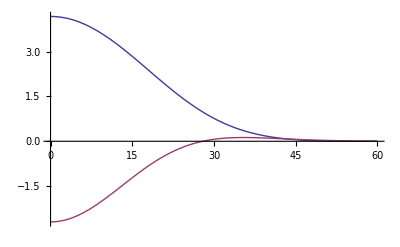

```mathematica
Plot[{Re[(4.18-I*2.70)*Exp[-(16-I*5.66)*4*0.66^2*Sin[t*Pi/360]^2]],Im[(4.18-I*2.70)*Exp[-(16-I*5.66)*4*0.66^2*Sin[t*Pi/360]^2]]},{t,0,60}]
```

```mathematica
Clear[σ,ρ,β]
```

{σ→3.82434,βre→14.1782}

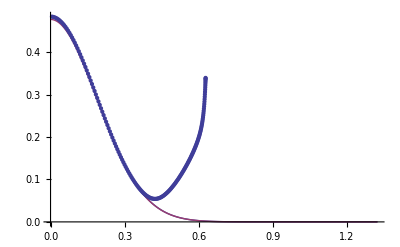

```mathematica
Npts=50;
FindFit[Transpose[{pp210[[1;;Npts,1]],Abs[pp210[[1;;Npts,2]]]}],κ/ℏc σ/(4 Pi) Exp[-βre q^2],{σ,βre},q]
Show[Plot[κ/ℏc σ/(4 Pi) Exp[-βre q^2]/.%,{q,0,2 P}],Plot[Abs[(2.50-I 2.93) Exp[-(14.15-I 6.33) q^2] (2 I κ ℏc)],{q,0,2 P},PlotStyle->ColorData[1,2]],ListPlot[Transpose[{pp210[[All,1]],Abs[pp210[[All,2]]]}]],PlotRange->All]
```

```mathematica
Abs[pp210[[1,2]]]
```

0.483834

{ρ→1.23114,βim→-6.4596}

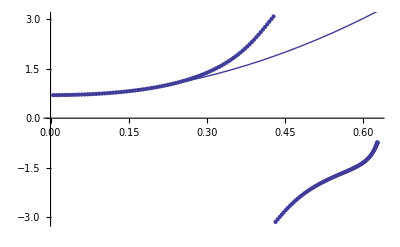

```mathematica
FindFit[Transpose[{pp210[[1;;Npts,1]],Arg[pp210[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{pp210[[All,1]],Arg[pp210[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 P}]]
```

```mathematica
σ=3.8243362284391385;
ρ=1.2311421763594046;
β=3.1880250907249894-1.4524697490347995 I;
```

## Glauber

```mathematica
σ1=σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

(1.02185 (1-ⅈ ρ) σ)/β

```mathematica
σ
```

3.82434

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

151.688

## Add in First Order Correction

```mathematica
Γ[b_]:=σ1 Exp[-b^2/(4 β)]
```

```mathematica
Γ[0]
```

1.58448-0.78725 ⅈ

```mathematica
U[q_]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-Γ[b]],{b,0,Infinity}]
```

```mathematica
U[0]
```

-97.4768-15.1543 ⅈ

Wallace parameterizes it as a gaussian in q, so we should check the validity of that assertion:

```mathematica
Quiet[Table[{q,Abs[U[Sqrt[q]]]},{q,0.001,1.001,.1}]]
```

{{0.001,98.3276},{0.101,70.8128},{0.201,50.6675},{0.301,36.0329},{0.401,25.5203},{0.501,18.0912},{0.601,12.9647},{0.701,9.54253},{0.801,7.34477},{0.901,5.97041},{1.001,5.09504}}

```mathematica
interp1=Interpolation[{{0.001,98.32763976229225},{0.101,70.81278495696812},{0.201,50.6675191879384},{0.30100000000000005,36.03294527833977},{0.401,25.520334827981625},{0.501,18.091157370259893},{0.6010000000000001,12.964736159178019},{0.7010000000000001,9.54252689167767},{0.801,7.3447707468069465},{0.901,5.97041281526392},{1.001,5.095037226651615}}];
```

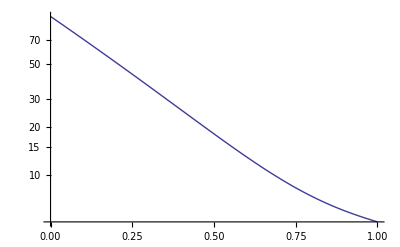

```mathematica
Quiet[LogPlot[interp1[t],{t,0,1}]]
```

The magnitude seems to be well approximated by a gaussian.

```mathematica
Quiet[Table[{q,Arg[U[Sqrt[q]]]},{q,0,1,.01}]]
```

{{0.,-2.98736},{0.01,-2.98307},{0.02,-2.97893},{0.03,-2.97496},{0.04,-2.97116},{0.05,-2.96752},{0.06,-2.96406},{0.07,-2.96077},{0.08,-2.95766},{0.09,-2.95473},{0.1,-2.95199},{0.11,-2.94944},{0.12,-2.94708},{0.13,-2.94492},{0.14,-2.94296},{0.15,-2.9412},{0.16,-2.93966},{0.17,-2.93832},{0.18,-2.93721},{0.19,-2.93632},{0.2,-2.93565},{0.21,-2.93522},{0.22,-2.93503},{0.23,-2.93508},{0.24,-2.93537},{0.25,-2.93592},{0.26,-2.93673},{0.27,-2.9378},{0.28,-2.93914},{0.29,-2.94076},{0.3,-2.94266},{0.31,-2.94484},{0.32,-2.94733},{0.33,-2.95011},{0.34,-2.9532},{0.35,-2.9566},{0.36,-2.96033},{0.37,-2.96438},{0.38,-2.96876},{0.39,-2.97349},{0.4,-2.97857},{0.41,-2.984},{0.42,-2.98979},{0.43,-2.99595},{0.44,-3.00249},{0.45,-3.00941},{0.46,-3.01671},{0.47,-3.02442},{0.48,-3.03252},{0.49,-3.04103},{0.5,-3.04996},{0.51,-3.0593},{0.52,-3.06906},{0.53,-3.07925},{0.54,-3.08988},{0.55,-3.10093},{0.56,-3.11242},{0.57,-3.12435},{0.58,-3.13672},{0.59,3.13366},{0.6,3.12041},{0.61,3.10673},{0.62,3.09262},{0.63,3.07809},{0.64,3.06313},{0.65,3.04776},{0.66,3.03198},{0.67,3.01581},{0.68,2.99925},{0.69,2.98232},{0.7,2.96504},{0.71,2.94742},{0.72,2.92947},{0.73,2.91122},{0.74,2.89269},{0.75,2.87389},{0.76,2.85486},{0.77,2.8356},{0.78,2.81616},{0.79,2.79655},{0.8,2.7768},{0.81,2.75693},{0.82,2.73697},{0.83,2.71695},{0.84,2.6969},{0.85,2.67683},{0.86,2.65679},{0.87,2.63678},{0.88,2.61684},{0.89,2.59698},{0.9,2.57724},{0.91,2.55762},{0.92,2.53816},{0.93,2.51887},{0.94,2.49976},{0.95,2.48085},{0.96,2.46216},{0.97,2.4437},{0.98,2.42547},{0.99,2.4075},{1.,2.38978}}

```mathematica
interp2=Interpolation[{{0.,-2.9873614327729356},{0.01,-2.983067075076218},{0.02,-2.978932882776467},{0.03,-2.9749617442068006},{0.04,-2.9711566323894867},{0.05,-2.9675206080462315},{0.06,-2.964056822435328},{0.07,-2.9607685201605585},{0.08,-2.9576590420667928},{0.09,-2.954731828126964},{0.1,-2.95199042035892},{0.11,-2.9494384657465034},{0.12,-2.9470797191501212},{0.13,-2.944918046196124},{0.14,-2.942957426129427},{0.15,-2.9412019546115236},{0.16,-2.93965584644264},{0.17,-2.9383234381817602},{0.18,-2.937209190648951},{0.19,-2.936317691244455},{0.2,-2.9356536561057993},{0.21,-2.9352219320252457},{0.22,-2.9350274980857414},{0.23,-2.935075466993051},{0.24,-2.935371086025859},{0.25,-2.935919737557642},{0.26,-2.936726939084304},{0.27,-2.9377983426760634},{0.28,-2.9391397338000997},{0.29,-2.940757029392926},{0.3,-2.9426562751137304},{0.31,-2.944843641665295},{0.32,-2.9473254200719032},{0.33,-2.9501080157927886},{0.34,-2.953197941540247},{0.35000000000000003,-2.9566018086619734},{0.36,-2.9603263169377265},{0.37,-2.9643782426311867},{0.38,-2.9687644246291667},{0.39,-2.9734917484924086},{0.4,-2.978567128235406},{0.41000000000000003,-2.9839974856474862},{0.42,-2.9897897269641853},{0.43,-2.995950716697368},{0.44,-3.0024872484351723},{0.45,-3.0094060124294275},{0.46,-3.016713559799462},{0.47000000000000003,-3.024416263198056},{0.48,-3.032520273808559},{0.49,-3.0410314745728853},{0.5,-3.049955429589077},{0.51,-3.059297329665385},{0.52,-3.069061934076139},{0.53,-3.079253508633809},{0.54,-3.0898757602720996},{0.55,-3.1009317684269075},{0.56,-3.1124239136053777},{0.5700000000000001,-3.124353803647532},{0.58,-3.136722198308855},{0.59,3.1336563742556076},{0.6,3.1204124651308964},{0.61,3.106733623063128},{0.62,3.0926232388972115},{0.63,3.078085922422926},{0.64,3.063127567133647},{0.65,3.0477554085629275},{0.66,3.03197807461514},{0.67,3.015805626271033},{0.68,2.9992495870547096},{0.6900000000000001,2.9823229597016065},{0.7000000000000001,2.9650402285728985},{0.71,2.947417346523966},{0.72,2.9294717051547328},{0.73,2.911222087646803},{0.74,2.892688603722293},{0.75,2.8738926066351316},{0.76,2.854856592516925},{0.77,2.835604082833322},{0.78,2.816159491147316},{0.79,2.7965479758160665},{0.8,2.7767952806492144},{0.81,2.756927565911674},{0.8200000000000001,2.7369712323459083},{0.8300000000000001,2.716952741103789},{0.84,2.6968984326057295},{0.85,2.676834347378577},{0.86,2.656786051861973},{0.87,2.6367784720186775},{0.88,2.616835737345425},{0.89,2.5969810375686815},{0.9,2.577236493939285},{0.91,2.5576230466282115},{0.92,2.5381603592906297},{0.93,2.5188667414252284},{0.9400000000000001,2.4997590887269605},{0.9500000000000001,2.4808528412293414},{0.96,2.4621619586690775},{0.97,2.4436989121908317},{0.98,2.4254746912493363},{0.99,2.407498824362892},{1.,2.3897794122270413}}];
```

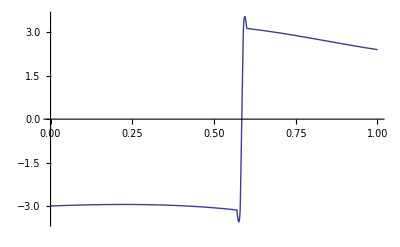

```mathematica
Quiet[Plot[interp2[t],{t,0,1}]]
```

```mathematica
Quiet[U[.1]]
```

-94.2925-15.0743 ⅈ

```mathematica
γ=100^2*Quiet[(Log[U[0]]-Log[U[0.01]])]
```

3.25052-0.437268 ⅈ

```mathematica
Z=U[0]/(-I*4*Pi*σ1*β)(*Unitless*)
```

1.09406-0.638 ⅈ

Here are a bunch of parameters that Wallace has defined in his paper.

```mathematica
γ1:=γ*β/(γ+β)(*(c/GeV)^2*)
αnL[n_,L_]:=If[n==1,(2*(γ+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ+B)^-1+(γ1+B)^-1+L*(β+B)^-1)^-1,If[n==3,(2*(γ1+B)^-1+L*(β+B)^-1)^-1]]]
an[n_]:=If[n==1,(γ+B)^-2,If[n==2,-2*σ1*(γ1/γ)*(γ+B)^-1*(γ1+B)^-1,If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-2]]]
bn[n_]:=If[n==1,(γ+B)^-3,If[n==2,-σ1*(γ1/γ)*(γ1+B)^-1*(γ+B)^-1*((1-B*γ1/(β*(B+γ1)))/(γ+B)+(1-γ1/β)/(γ1+B)),If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-3*(1-B*γ1/(β*(B+γ1)))*(1-γ1/β)]]]
γ2:=γ*β/(β+2*γ)(*(c/GeV)^2*)
βnL[n_,L_]:=If[n==1,((γ/2+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ2/2+B)^-1+L*(β+B)^-1)^-1]]
cn[n_]:=If[n==1,(γ-2*B)*(γ+2*B)^-2,If[n==2,-σ1(γ2/γ1)*(γ2+2*B)^-1*(1-2*γ2/γ+2*(γ2)^2/(γ*(γ2+2*B)))]]
dn[n_]:=If[n==1,γ*(γ+2*B)^-3,If[n==2,
-σ1*(γ)^-2*(γ2/(γ2+2*B))^3]]
```

```mathematica
FO1[q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO*(β*σ1*Z)^2/(2*(2*Pi*(B+β))^(1/2))*Sum[Binomial[A-2,L]*(-σ1*β/(B+β))^L*Sum[αnL[n,L]*(an[n]-4*αnL[n,L]*bn[n]*(1-αnL[n,L]q^2))*Exp[-αnL[n,L]*q^2],{n,1,3}],{L,0,A-2}]*ℏc
```

```mathematica
FD1[q_(*c/GeV*)]:=A*Fcm[q]*ηD*(β*σ1*Z)^2/(2*γ*Sqrt[2*Pi*γ])*Sum[Binomial[A-1,L]*(-σ1*β/(B+β))^L*Sum[βnL[n,L]*(cn[n]-4*βnL[n,L]*dn[n]*(1-βnL[n,L]*q^2))*Exp[-βnL[n,L]*q^2],{n,1,2}],{L,0,A-1}]*ℏc
```

```mathematica
Im[FO1[0]+FD1[0]]/Im[F0[0]+FO1[0]+FD1[0]]
```

-0.0714002

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]+F0[0]]
```

151.688

-10.1088

141.579

```mathematica
FO1[0]
```

0.0139093+0.113072 ⅈ

```mathematica
FD1[0]
```

-0.240451-0.321647 ⅈ